## Setup

```mathematica
Get["FunKit`"]
```

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

```mathematica
fields= <|
"cField"-> {ϕ[p]},
"Grassmann"->{}
|>;
truncation=<|
GammaN->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}},
Propagator->{{ϕ,ϕ}},
Rdot->{{ϕ,ϕ}},
S->{{ϕ,ϕ},{ϕ,ϕ,ϕ,ϕ}}
|>;

Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"DiagramStyling"->diagramStyling
|>;
FSetGlobalSetup[Setup];

FunKitDebugLevel[0];
```

## DSE


2 -Graphics-+12 -Graphics--4 -Graphics-+12 -Graphics-

-Graphics-

```mathematica
DSE2P=FTakeDerivatives[MakeDSE[Setup,ϕ[i1]],{ϕ[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

24 -Graphics--36 -Graphics-+12 -Graphics-+8 -Graphics-+4 -Graphics-+12 -Graphics-

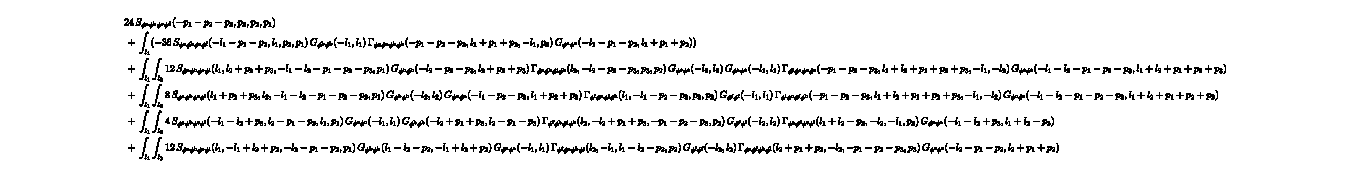

```mathematica
symmetryP4=Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]];
DSE4P=FTakeDerivatives[MakeDSE[Setup,ϕ[i1]],{ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FSimplify[#,"Symmetries"->{symmetryP4,{i1,i2,i3,i4}}]&//FPlot//FRoute//FPrint;
```

```mathematica
symmetryP6={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4,5,6}]],{i1,i2,i3,i4,i5,i6}};
DSE6P=FTakeDerivatives[MakeDSE[Setup,ϕ[i1]],{ϕ[i2],ϕ[i3],ϕ[i4]},"Symmetries"->symmetryP6]//FTruncate//FSimplify;
DSE6P=FTakeDerivatives[DSE6P,{ϕ[i5],ϕ[i6]},"Symmetries"->symmetryP6]//FTruncate//FSimplify[#,"Symmetries"->symmetryP6]&//FPlot//FRoute//FPrint;
```

-36 -Graphics-+72 -Graphics-+12 -Graphics-+24 -Graphics-+12 -Graphics-+12 -Graphics-+12 -Graphics-+24 -Graphics-+24 -Graphics-+12 -Graphics-+12 -Graphics--24 -Graphics--48 -Graphics--24 -Graphics--24 -Graphics--24 -Graphics-

-Graphics-

## fRG

```mathematica
fRG2P=FTakeDerivatives[Setup,WetterichEquation,{ϕ[i1],ϕ[i2]}]//FTruncate//FPlot//FRoute//FPrint;
```

--Graphics-/2

-Graphics-

```mathematica
fRG4P=FTakeDerivatives[Setup,WetterichEquation,{ϕ[i1],ϕ[i2],ϕ[i3],ϕ[i4]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
```

-Graphics-+-Graphics-+-Graphics-

-Graphics-